```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
rdata= Drop[Import["torsion_test_k1_lc_torque_diagram.txt","Data"],1];
rdata[[All,{2,3}]]*=-100000.0;
```

```mathematica
rdata
```

{{0.000100000000000000005,35.9932,-0.0000581049},{0.000263665089873035829,35.9933,-0.000403968},{0.000695192796177560479,35.9942,-0.00280831},{0.00183298071083243556,36.0001,-0.0195192},{0.0048329302385717518,36.0382,-0.135506},{0.0127427498570313342,36.1875,-0.933752},{0.0335981828628378124,35.8552,-6.23297},{0.0885866790410082261,52.4321,-37.7936},{0.233572146909012124,152.153,-198.212},{0.615848211066026052,283.195,-1115.84},{1.62377673918872101,353.757,-7393.8},{4.28133239871939608,371.655,-50213.5},{11.2883789168468827,374.608,-346945.},{29.7635144163131322,375.042,-2.40957×10^6},{78.4759970351460652,375.105,-1.67487×10^7},{206.913808111479,375.114,-1.16434×10^8},{545.559478116851437,375.115,-8.09436×10^8},{1438.44988828766009,375.115,-5.62714×10^9},{3792.69019073224581,375.115,-3.91195×10^10},{10000.,375.115,-2.71956×10^11}}

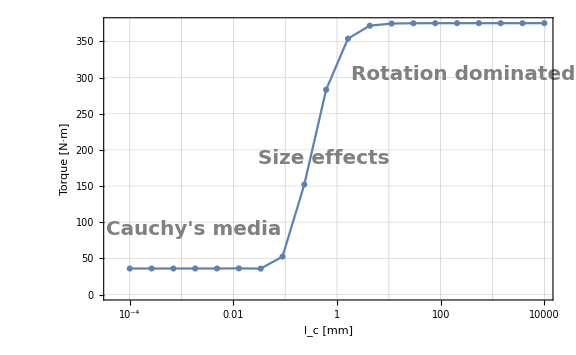

```mathematica
ListLogLinearPlot[rdata[[All,{1,2}]],Joined->True, PlotMarkers->Automatic,Frame->True,GridLines->{{0.0001,0.001,0.01,0.1,1.0,10.0,100.0,1000.0,10000.0},Automatic},FrameLabel->{Style["l_c [mm]",24],Style["Torque [N·m]",24]},FrameStyle->Directive[{Black,Italic,18}],ImageSize->Large,Epilog->{Text[Style["Cauchy's media",Bold,Gray,Italic,20],Scaled[{0.2,0.25}]],Text[Style["Size effects",Bold,Gray,Italic,20],Scaled[{0.49,0.5}]],Text[Style["Rotation dominated",Bold,Gray,Italic,20],Scaled[{0.8,0.8}]]}]
```

```mathematica
Cross[{sx,sy,0},{x1,x2,x3}]//MatrixForm
```

(sy x3
-sx x3
-sy x1+sx x2)